# Figure 2 and 4

## Wang Pha

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
tmp=ReadList["WP-data.txt"];
```

```mathematica
sumall=Import["WPsummary.csv","CSV"];
```

```mathematica
Pid={"M001","M003","M005","M006","M007","M011","M012","M013","M014","M021","M023","M024","M026","M030","M032","M035","M036","M037","M039"};
PidIndx=Thread[Pid->Range[Length@Pid]]
```

{M001→1,M003→2,M005→3,M006→4,M007→5,M011→6,M012→7,M013→8,M014→9,M021→10,M023→11,M024→12,M026→13,M030→14,M032→15,M035→16,M036→17,M037→18,M039→19}

```mathematica
DATLength={11,5,9,8,9,6,14,9,12,9,7,8,11,6,7,8,11,20,13};
```

```mathematica
times={0,2,4,6,8,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162};
```

```mathematica
DetecLim={8.58433,8.17167,7.82321,7.84757,7.65128,7.8396,7.83149,7.80618,7.84757,7.88536,8.5666,7.8396,7.84757,7.81478,7.8996,8.94227,7.8554,7.92675,7.8996};
```

```mathematica
ExtractDAT[indx_]:=Thread[{times[[1;;DATLength[[indx]]]],DAT[[indx,1;;DATLength[[indx]]]]}]
```

```mathematica
ExtractPar[indx_]:=Module[{simdat,tls},simdat=(Select[sumall,StringTake[First@#,7+(IntegerDigits[indx]//Length)]=="y_pred["<>ToString@indx&]//Quiet)[[1;;DATLength[[indx]],{5,6,7}]]ᵀ;
tls=times[[1;;DATLength[[indx]]]];
{tls,#}ᵀ&/@simdat
];
```

```mathematica
ExtractPar2[indx_]:=Module[{simdat,tls},simdat=(Select[sumall,StringTake[First@#,12+(IntegerDigits[indx]//Length)]=="ySplit_pred["<>ToString@indx&]//Quiet)[[1;;DATLength[[indx]],{5,6,7}]]ᵀ;
tls=times[[1;;DATLength[[indx]]]];
{tls,#}ᵀ&/@simdat
];
```

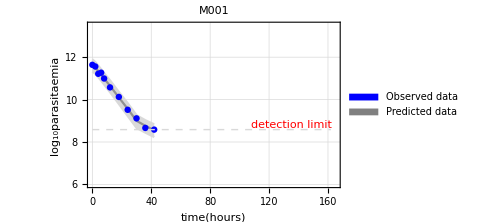

```mathematica
ListPlot[ExtractPar[1]~Join~{ExtractDAT[1]},Joined->{True,True,True,False},PlotRange->{{0,165},{6,13.5}},Frame->True,GridLines->Automatic,Filling->{1->{3}},FillingStyle ->{LightGray},PlotStyle->{LightGray,{Darker@LightGray},LightGray,Blue},FrameLabel->{Style["time(hours)",FontFamily->"Times New Roman",Bold,FontSize->12],Style["log_10parasitaemia",FontFamily->"Times New Roman",Bold,FontSize->12]},PlotLegends->Placed[SwatchLegend[{Blue,Gray},{"Observed data","Predicted data"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.7,0.95},{0.15,1}}],Epilog->{Dashed,LightGray,Line[{{0,DetecLim[[1]]},{162,DetecLim[[1]]}}],Red,Text["detection limit",{135,DetecLim[[1]]+0.2}]},PlotLabel->Pid[[1]],ImageSize->Medium]
```

```mathematica
PlotOutput[indx_Integer]:=ListPlot[ExtractPar[indx]~Join~{ExtractDAT[indx]},Joined->{True,True,True,False},PlotRange->{{0,24*6},{6,13.5}},Frame->True,GridLines->Automatic,Filling->{1->{3}},FillingStyle ->{LightGray},PlotStyle->{LightGray,{Darker@LightGray},LightGray,Blue},FrameLabel->{Style["time(hours)",FontFamily->"Times New Roman",Bold,FontSize->12],Style["log_10parasitaemia",FontFamily->"Times New Roman",Bold,FontSize->12]},PlotLegends->Placed[SwatchLegend[{Blue,Gray},{"Observed data","Predicted data"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.7,0.95},{0.15,1}}],Epilog->{Dashed,LightGray,Line[{{0,DetecLim[[indx]]},{162,DetecLim[[indx]]}}],Red,Text["detection limit",{125,DetecLim[[indx]]}]},PlotLabel->Pid[[indx]],ImageSize->Medium]
```

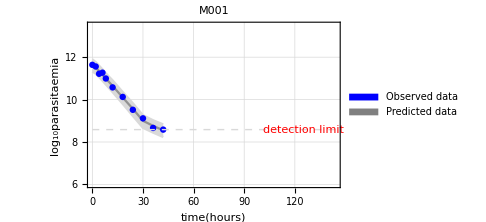
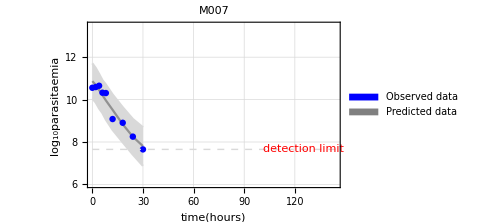
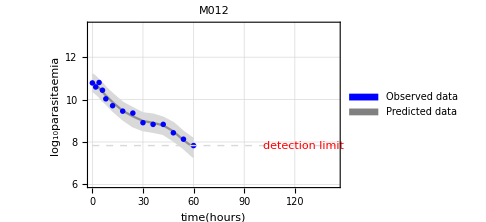
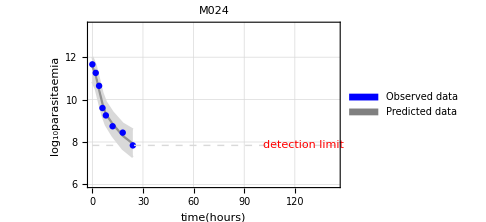

```mathematica
WPGr=PlotOutput[#/.PidIndx]&/@{"M001","M007","M012","M024"}
```

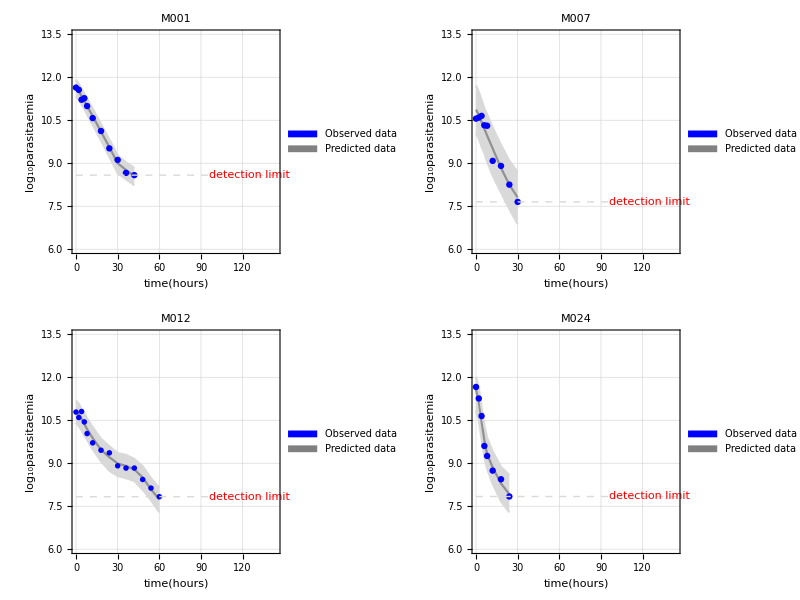
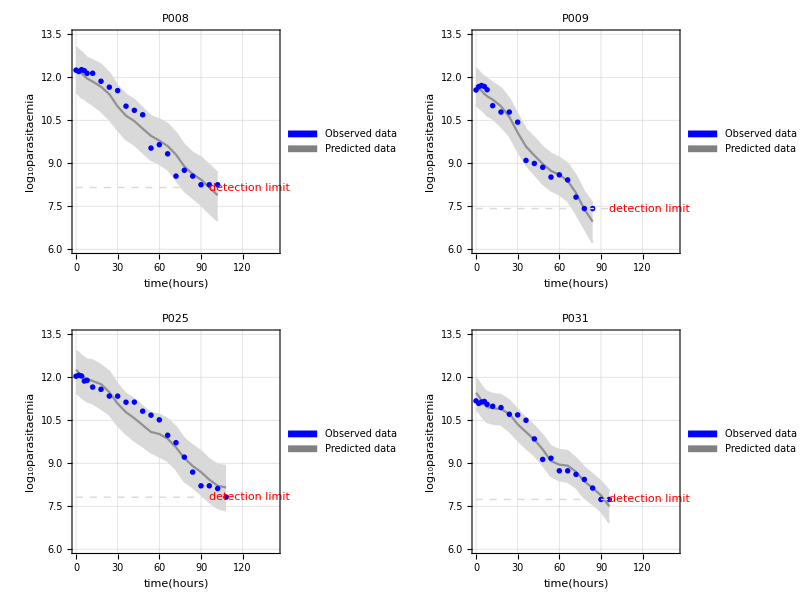
A) Wang Pha
-Graphics-
B) Pailin
-Graphics-

```mathematica
Column[{Style["A) Wang Pha",Bold,FontSize->18],Grid[Partition[WPGr,2]],Style["B) Pailin",Bold,FontSize->18],Grid[Partition[PLGr,2]]},Frame->All]
```

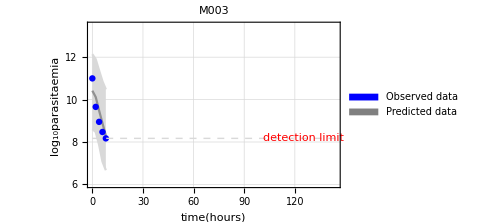
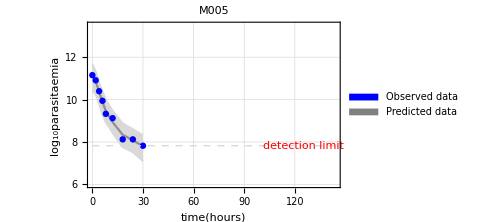
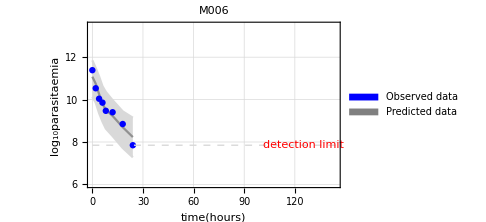
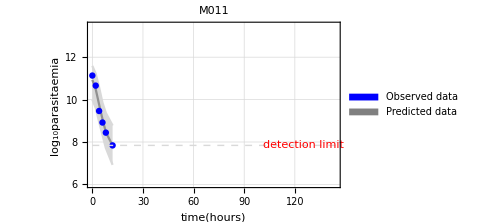
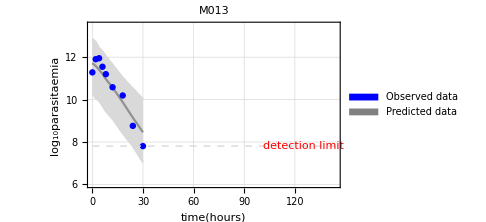
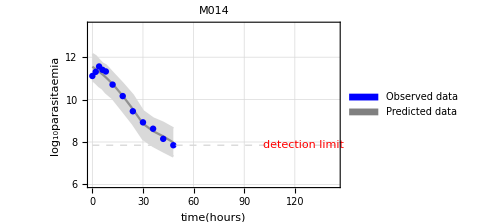
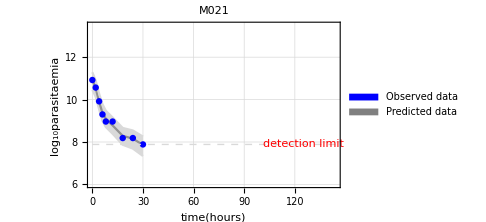
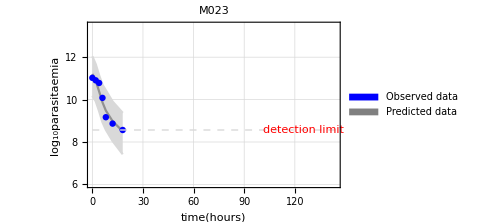
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[Partition[PlotOutput/@Range[19],UpTo[4]],Frame->All,ItemSize->All]
```

```mathematica
PlotOutput2[indx_Integer]:=ListPlot[
ExtractPar2[indx]~Join~{ExtractDAT[indx]}~Join~ExtractPar[indx],
Joined->{True,True,True,False,True,True,True},PlotRange->{{0,24*6},{6,13.5}},
Frame->True,GridLines->Automatic,
Filling->{1->{{3},LightGreen},5->{{7},LightPurple}},
PlotStyle->{LightGreen,Green,LightGreen,Black,LightPurple,Lighter@Lighter@Purple,LightPurple},FrameLabel->{Style["time(hours)",FontFamily->"Times New Roman",Bold,FontSize->12],Style["log_10parasitaemia",FontFamily->"Times New Roman",Bold,FontSize->12]},PlotLegends->Placed[SwatchLegend[{Black,Lighter@Lighter@Purple,Green},{"Observed data (every 24 hrs)","Predicted data (every 24 hrs)","Predicted data (every 12 hrs)"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.5,0.95},{0.15,1}}],Epilog->{Dashed,LightGray,Line[{{0,DetecLim[[indx]]},{162,DetecLim[[indx]]}}],Red,Text["detection limit",{125,DetecLim[[indx]]}]},PlotLabel->Pid[[indx]],ImageSize->Medium]
```

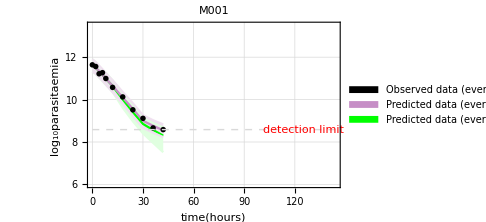

```mathematica
PlotOutput2[1]
```

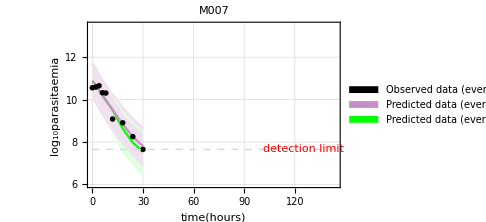
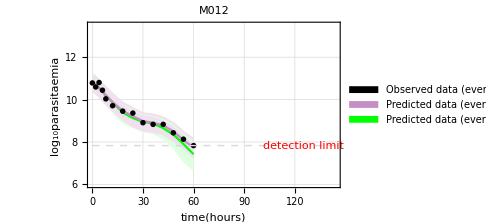
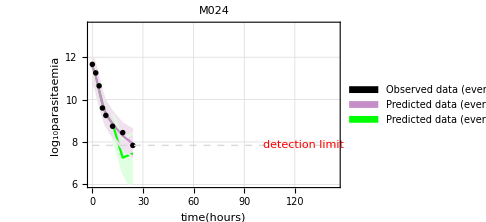
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WPGr2=PlotOutput2[#/.PidIndx]&/@{"M001","M007","M012","M024"}
```

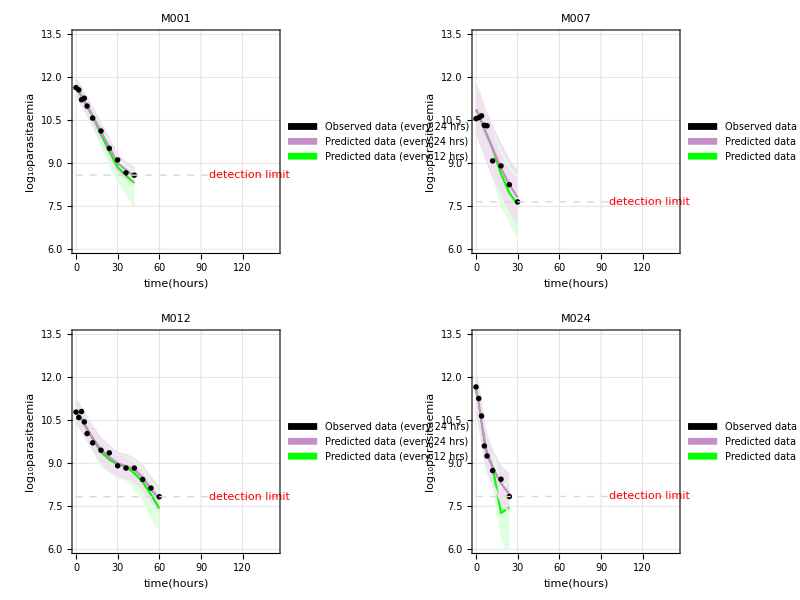
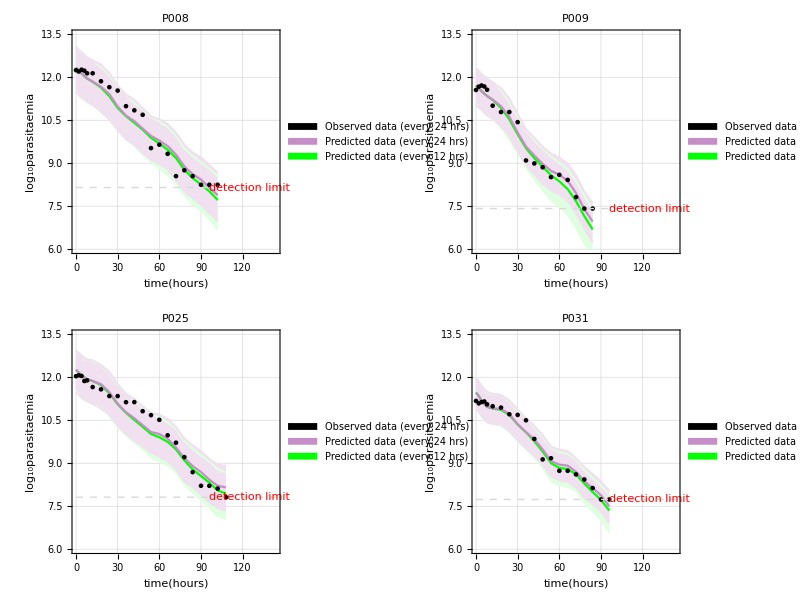
A) Wang Pha
-Graphics-
B) Pailin
-Graphics-

```mathematica
Column[{Style["A) Wang Pha",Bold,FontSize->18],Grid[Partition[WPGr2,2]],Style["B) Pailin",Bold,FontSize->18],Grid[Partition[PLGr2,2]]},Frame->All]
```

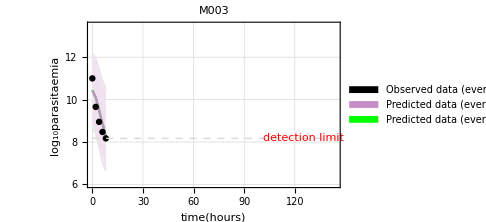
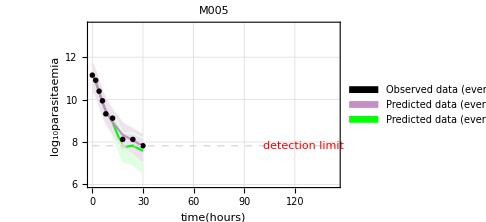
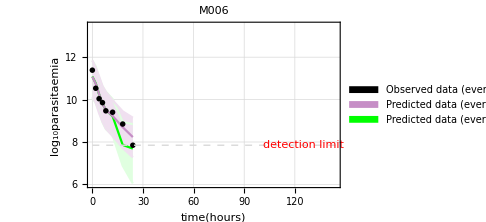
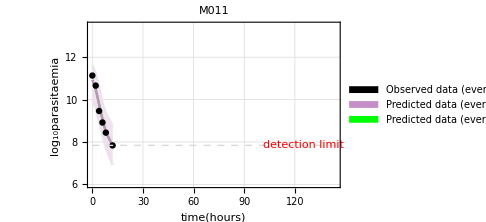
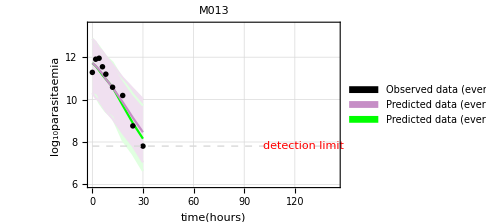
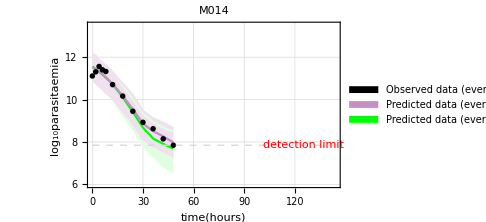
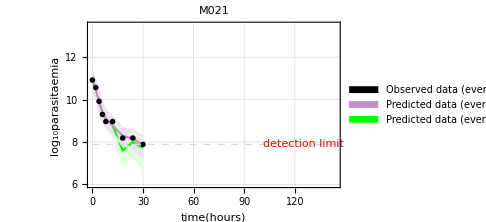
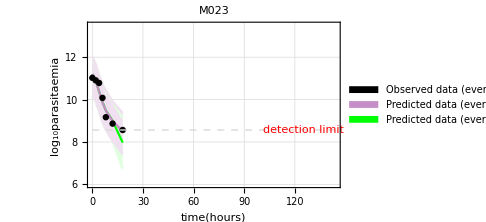
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[(PlotOutput2/@Range[19])//Partition[#,UpTo[4]]&,Frame->All]
```